## Equilibrium calculation

```mathematica
A[α_,γ_]:=(1-γ)/(α γ);
k[α_,γ_,r_]:=(r+1)/(A[α,γ] (r-1)+r)-1;
```

```mathematica
q2=3;q1=2;β=2;α=0.8;
```

#### Type 1 conformists

```mathematica
eqtype1conform[r_,α_,β_,γ_]:=1/(k[α,γ,r]^(1/β)+1)
```

```mathematica
type1confdata=Import[NotebookDirectory[]<>"type1conf.csv","CSV"];
```

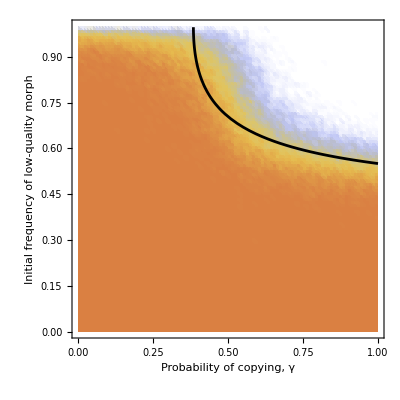

```mathematica
Show[ListDensityPlot[type1confdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype1conform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 1 anticonformists

```mathematica
α=2.8;
```

```mathematica
eqtype1anticonform[r_,α_,β_,γ_]:=1/(k[α,γ,r]^(1/β)+1)
```

```mathematica
type1anticonfdata=Import[NotebookDirectory[]<>"typeI_anticonformist_b-2/out.csv","CSV"];
```

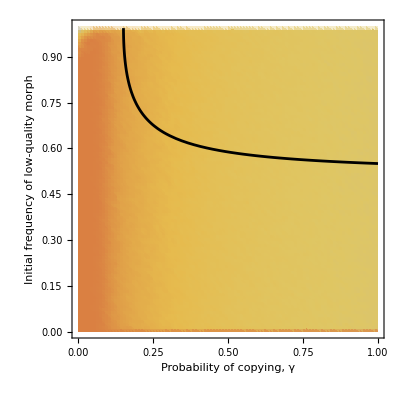

```mathematica
Show[ListDensityPlot[type1anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype1anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 conformists

```mathematica
α=0.6;f=0.83;
```

```mathematica
eqtype2conform[r_,α_,β_,γ_]:=If[0.45<γ&&γ≤0.51,(1/(k[α,γ,r]+1)-f)/(1-f),If[γ≥0.51,0.5,None]]
```

```mathematica
type2confdata=Import[NotebookDirectory[]<>"typeII_conformist_f1.2/out.csv","CSV"];
```

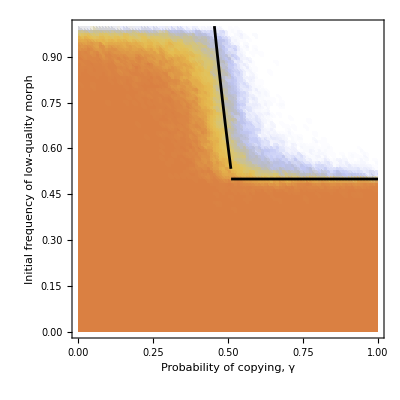

```mathematica
Show[ListDensityPlot[type2confdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2conform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 anticonformists

```mathematica
α=1.1;f=0.83;
```

```mathematica
eqtype2anticonform[r_,α_,β_,γ_]:=If[γ≥0.36,0.5,(1/(k[α,γ,r]+1)-f)/(1-f)]
```

```mathematica
type2anticonfdata=Import[NotebookDirectory[]<>"typeII_anticonformist_f1.2/out.csv","CSV"];
```

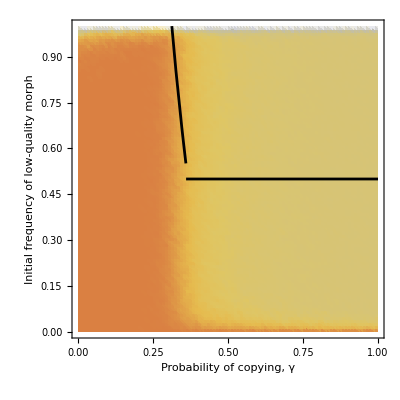

```mathematica
Show[ListDensityPlot[type2anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 mixed

```mathematica
α=0.5;f=0.83;
```

```mathematica
eqtype2mixed[r_,α_,β_,γ_]:=If[
γ<0.5,None,
If[γ>0.5&&γ≤0.53,1/(k[α,γ,r]+1),
If[γ≥0.53&&γ<0.56,(1/(k[α,γ,r]+1)-f)/(1-f),0.5]]]
```

```mathematica
type2mixeddata=Import[NotebookDirectory[]<>"typeII_mixed_f1.2/out.csv","CSV"];
```

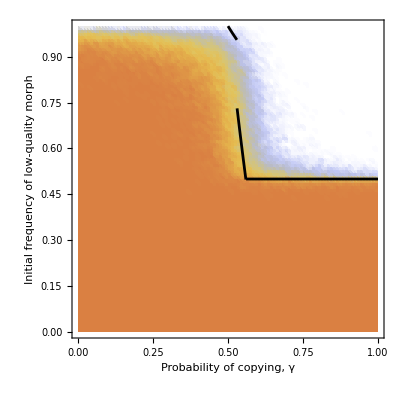

```mathematica
Show[ListDensityPlot[type2mixeddata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2mixed[q2/q1,α,β,γ],{γ,0,1},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```